## Structured objects

```mathematica
List[]
```

{}

```mathematica
{1,2,3,4,5,6}
```

{1,2,3,4,5,6}

```mathematica
{} //FullForm
```

List[]

```mathematica
Clear[list]
```

```mathematica
list = {{a},{b},{c},{d}}
```

{{a},{b},{c},{d}}

```mathematica
Part[list,1]
```

{a}

```mathematica
Part[list, -1]
```

{d}

```mathematica
list[[2]]
```

{b}

```mathematica
Append[list,{e}]
```

{{a},{b},{c},{d},{e}}

```mathematica
Append[list,{{f},{g},{h}}]
```

{{a},{b},{c},{d},{{f},{g},{h}}}

## Map

```mathematica
Clear[list]
```

```mathematica
list= {{1,2,3},{6,7,8}}
```

{{1,2,3},{6,7,8}}

```mathematica
Map[f,list]
```

{f[{1,2,3}],f[{6,7,8}]}

```mathematica
Map[f,list,{2}] (*Apply to level 2 only*)
```

{{f[1],f[2],f[3]},{f[6],f[7],f[8]}}

```mathematica
Map[f,list,2] (*Apply to all level up 2*)
```

{f[{f[1],f[2],f[3]}],f[{f[6],f[7],f[8]}]}

```mathematica
Flatten[{1,{2,3},{{4,5}}},1]
```

{1,2,3,{4,5}}

```mathematica
Flatten[{1,{2,3},{{4,5}}},2]
```

{1,2,3,4,5}

### Symbols generating lists

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[10^4]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,9920,9961,9962,9963,9964,9965,9966,9967,9968,9969,9970,9971,9972,9973,9974,9975,9976,9977,9978,9979,9980,9981,9982,9983,9984,9985,9986,9987,9988,9989,9990,9991,9992,9993,9994,9995,9996,9997,9998,9999,10000}
 |  |  |  |

```mathematica
ConstantArray[1, 20]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ConstantArray[1, {5,5}] //MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1)

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Array[f,10,5]
```

{f[5],f[6],f[7],f[8],f[9],f[10],f[11],f[12],f[13],f[14]}

```mathematica
Array[f,{3,3}] //MatrixForm
```

(f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3])

```mathematica
Array[f[#1,#2]&, {3,3}] //MatrixForm
```

(f[1,1] | f[1,2] | f[1,3]
f[2,1] | f[2,2] | f[2,3]
f[3,1] | f[3,2] | f[3,3])

```mathematica
coordinates = CirclePoints[5]
```

{{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)}}

```mathematica
Alphabet["Arabic"]
```

{ا,ب,ت,ث,ج,ح,خ,د,ذ,ر,ز,س,ش,ص,ض,ط,ظ,ع,غ,ف,ق,ك,ل,م,ن,ه,و,ي}

```mathematica
Alphabet["Hindi"]
```

{अ,आ,इ,ई,उ,ऊ,ऋ,ए,ऐ,ओ,औ,क,ख,ग,घ,ङ,च,छ,ज,झ,ञ,ट,ठ,ड,ढ,ण,त,थ,द,ध,न,प,फ,ब,भ,म,य,र,ल,व,श,ष,स,ह}

```mathematica
list1 = CharacterRange["A","z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Length[list1]
```

58

```mathematica
Depth[list1]
```

2

```mathematica
Dimensions[list1]
```

{58}

```mathematica
list3 = {a,{b,c}}
```

{a,{b,c}}

```mathematica
Length[list3]
```

2

```mathematica
Dimensions[list3]
```

{2}

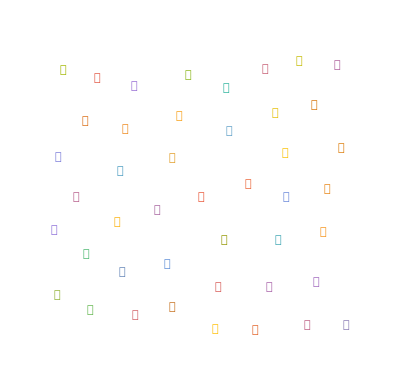

```mathematica
WordCloud[Alphabet["Hindi"]]
```

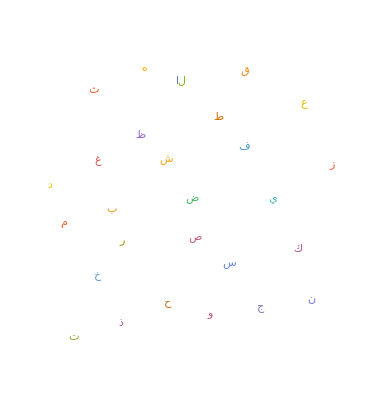

```mathematica
WordCloud[Alphabet["Arabic"]]
```

```mathematica
crescent := Image[Import["http://img.clipartall.com/crescent-moon-clip-art-crescent-moon-clip-art-700_700.jpg"]]
WordCloud[Alphabet["Arabic"],ColorNegate[crescent]]
-Graphics-
```

### Sparse array

```mathematica
SparseArray[1->5, 10]
```

SparseArray[<1>, {10}]

```mathematica
Normal[%]
```

{5,0,0,0,0,0,0,0,0,0}

## Associations

```mathematica
<||>
```

```mathematica
assoc = Association[a->1,b->2,c->3]
```

<|a→1,b→2,c→3|>

```mathematica
Keys[assoc]
Values[assoc]
```

{a,b,c}

{1,2,3}

```mathematica
assoc[a]
```

1

```mathematica
AssociationMap[f,{a,b,c,d}]
```

<|a→f[a],b→f[b],c→f[c],d→f[d]|>

```mathematica
Lookup[assoc, 10^6]; //AbsoluteTiming
```

{6.×10^-6,Null}